```mathematica
f[x_]:=Integrate[y^2/(Exp[y^2-x]-1),{y,0,Infinity}]
```

```mathematica
f[x]
```

1/4 √π PolyLog[3/2,ⅇ^x]

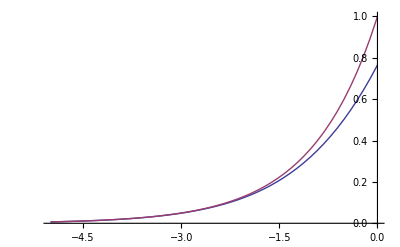

```mathematica
Plot[{-PolyLog[3/2,-Exp[x]],Exp[x]},{x,-5,0},PlotRange->All]
```

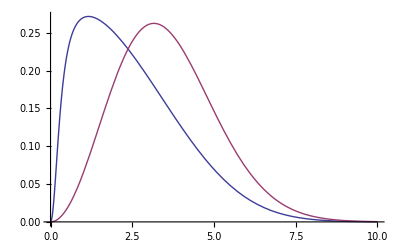

```mathematica
kT=10;n=-0.01;Plot[{v^2/(Exp[ v^2/kT-n]-1)/NIntegrate[V^2/(Exp[ V^2/kT-n]-1),{V,0,Infinity}],v^2 Exp[-v^2/kT]/NIntegrate[V^2 Exp[-V^2/kT],{V,0,Infinity}]},{v,0,10},PlotRange->All]
```

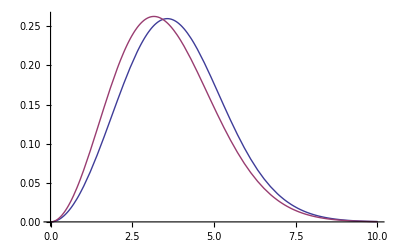

```mathematica
kT=10;n=-0.01;Plot[{v^2/(Exp[ v^2/kT-n]+1)/NIntegrate[V^2/(Exp[ V^2/kT-n]+1),{V,0,Infinity}],v^2 Exp[-v^2/kT]/NIntegrate[V^2 Exp[-V^2/kT],{V,0,Infinity}]},{v,0,10},PlotRange->All]
```